# Mathematica Notebook for Problem Set 2

Important note: Use Evaluation → Quit Kernel if you run into strange behavior.  Each command you run changes the environment and quitting the kernel will reset the environment / variables.

## Bifurcations

## Manipulating a curve

Manipulating a curve: the manipulate command creates a slider so that you can explore the impact of a parameter.

```mathematica
Manipulate[Plot[{r+x^2},{x,-3,3},PlotRange->{Automatic,{-3,6}}],{r,-2,2}]
(* I set the plot range so that the axes limits don't change as I adjust r.*)
```

I can define a function first, and plot that.  I do this two ways in the following block of code:

(1) I define f(x).  f will take inputs x.  The value of r is not assigned, though, and I can assign it using /.
/. allows us to replace an expression locally.  Here, I replace r with the Manipulate variable rval to let Mathematica know what to use for r.

(2) I define h(x,r).  Now h will take inputs x and r, with x coming from the plot command and r from the manipulate command.

```mathematica
f[x_] := r + x^2;
Manipulate[Plot[f[x]/.r->rval,{x,-3,3},PlotRange->{Automatic,{-3,6}}],{rval,-2,2}]
h[x_,r_] := r + x^2;
Manipulate[Plot[h[x,r],{x,-3,3},PlotRange->{Automatic,{-3,6}}],{r,-2,2}]
```

Plot two curves against each other, while manipulating one.

```mathematica
Manipulate[Plot[{Exp[-x],r-x},{x,-3,3},PlotRange->{Automatic,{-3,6}}],{r,0,2}]
```

## Plotting the shape of a bifurcation diagram

Plot the shape of a bifurcation diagram: think of both the state variable and the parameters as inputs to a function.   The fixed points are given by the zero-contour of that function.
Unlike with the Manipulate command, where I needed to use a /. to let Mathematica know how to replace r, the ContourPlot command is able to treat r like a variable (even though it isn't an explicit input to f(x)).

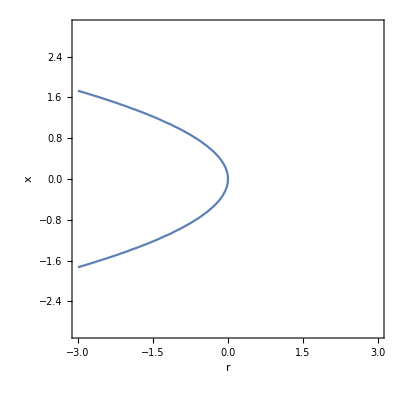

```mathematica
f[x_]:= r+x^2
ContourPlot[f[x]==0,{r,-3,3},{x,-3,3},FrameLabel->{r,x}]
```

For formatting, contour plots are plotted in a "frame", but I often prefer "axes".

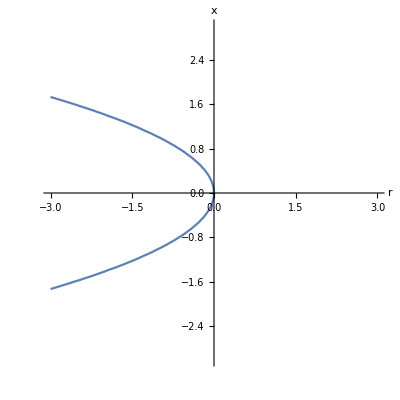

```mathematica
f[x_]:= r+x^2
ContourPlot[f[x]==0,{r,-3,3},{x,-3,3},Frame->None,Axes->True,AxesLabel->{r,x}]
```

```mathematica
f[x_]:=Sin[x]+r*ArcTan[x]
```

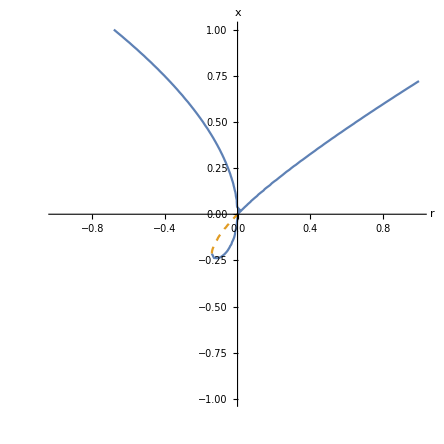

```mathematica
f[x_]:=-x^3+r^2-r*ArcTan[x]
ContourPlot[{Piecewise[{{f[x],f'[x]<0}},Indeterminate]==0,Piecewise[{{f[x],f'[x]>0}},Indeterminate]==0},{r,-1,1},{x,-1,1},ContourStyle->{{},{Dashed}},Frame->None,Axes->True,AxesLabel->{r,x}]
```

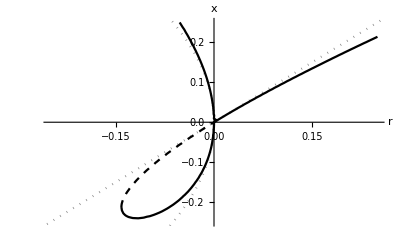

```mathematica
Show[
Plot[{-Sqrt[-x],Sqrt[-x]},{x,-.5,0},PlotStyle->{{Dotted,Gray}}],
Plot[{x},{x,-.5,.5},PlotStyle->{{Dotted,Gray}}],ContourPlot[{Piecewise[{{f[x],f'[x]<0}},Indeterminate]==0,Piecewise[{{f[x],f'[x]>0}},Indeterminate]==0},{r,-.25,.25},{x,-.25,.25},ContourStyle->{{Black},{Black,Dashed}},Frame->None,Axes->True,AxesLabel->{r,x}],PlotRange->{{-.25,.25},{-.25,.25}},AxesLabel->{r,x}]
```

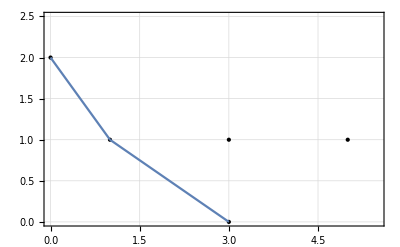

```mathematica
Show[ListPlot[{{1,1},{3,1},{5,1},{0,2},{3,0}},PlotStyle->{Black,PointSize[Large]},Frame->True,GridLines->Automatic,PlotRange->{{0,5.5},{0,2.5}}],
Plot[{2-x},{x,0,1}],Plot[{1-0.5(x-1)},{x,1,3}]]
```

```mathematica
ListPlot
```

Try to add stability information with color/dashing.  

I find this code extremely touchy.  If I use h[x_,r_] it doesn't work, so I'll use f[x_] (Mathematica  can treat a symbol as a variable even if it isn't an explicit option as a function input, so the "r" will still work for the contour plot).

To add the stability information, I create a piecewise function that is only defined when g'(x)<0 and a second piecewise function that is only defined with g'(x)>0.

I'll use a solid line to plot the first (stable fixed point) curve and a dashed one for the second (unstable fixed point) curve.

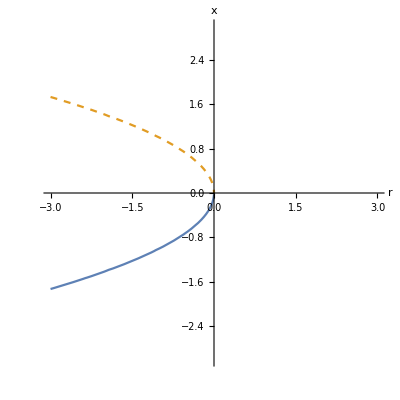

```mathematica
f[x_]:= r+x^2
ContourPlot[{Piecewise[{{f[x],f'[x]<0}},Indeterminate]==0,Piecewise[{{f[x],f'[x]>0}},Indeterminate]==0},{r,-3,3},{x,-3,3},ContourStyle->{{},{Dashed}},Frame->None,Axes->True,AxesLabel->{r,x}]
```

## Finding bifurcation points

Our necessary condition for a bifurcation is that we have a fixed point and the fixed point is non-hyperbolic.
Mathematically, that means we are looking for values of x and r that simultaneously satisfy f(x) = 0 (we have a fixed point) and f'(x) = 0 (the fixed point is non-hyperbolic).

```mathematica
f[x_]:=r + x^2
fp = Solve[f[x]==0,x]
possiblebifurcation = Solve[{f[x]==0,f'[x]==0},{x,r}]
```

{{x→-ⅈ √r},{x→ⅈ √r}}

{{x→0,r→0}}

## Stability Diagram: Example 1

Bifurcations occur when f(x) = 0 and f'(x) = 0 simultaneously (they occur at non-hyperbolic fixed points).
With two equations ({f(x)=0, f'(x) = 0}) that are simultaneously true, we can solve for two of the unknowns (for the example below, those are two of x, a,  or r.

Below, I solve for each unknown in terms of the other two.

Notice that I catch two solutions solving for x and r in terms of a.  The x -> 0 solution where r-> 0 and a is free doesn't appear in the other lines...

```mathematica
f[x_,r_,a_]:= r x -a x^2- x^3;
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,r}]
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,a}]
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{r,a}]
```

{{x→0,r→0},{x→-a/2,r→-a^2/4}}

{{x→-ⅈ √r,a→2 ⅈ √r},{x→ⅈ √r,a→-2 ⅈ √r}}

{{r→-x^2,a→-2 x}}

Version 1:  I plot the solution curves (of r) that I find in the first line:
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,r}]

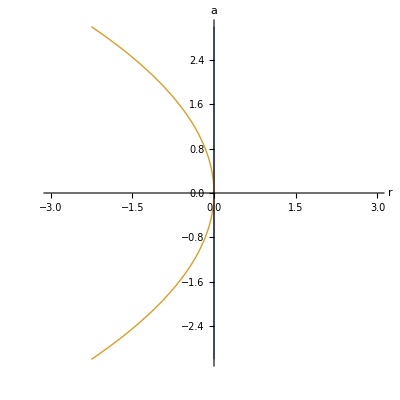

```mathematica
ContourPlot[{r==0, r == -a^2/4},{r,-3,3},{a,-3,3}, Frame->False,Axes->True,AxesLabel->{r,a},ContourStyle->Thick]
```

Version 2: I plot the r = 0 curve using ContourPlot.  I plot the second curve using the solution to 
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{r,a}]

I have r = -x^2 and a = -2x as one of the curves.  Using ParametricPlot, as I vary x the plotting command plots the (r,a) values associated with that specific x.  This traces out the parabola.

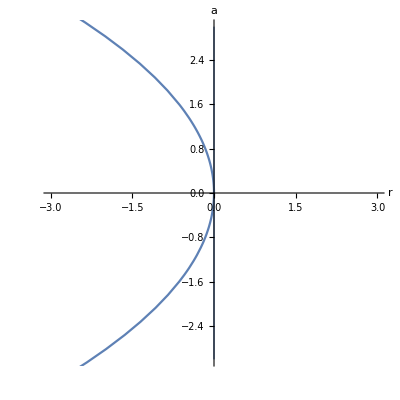

```mathematica
cp = ContourPlot[{r==0},{r,-3,3},{a,-3,3}, Frame->False,Axes->True,AxesLabel->{r,a},ContourStyle->Thick];
pp = ParametricPlot[{-x^2, -2x},{x,-3,3}];
Show[cp,pp]
```